```mathematica
Plot3D[x^2+y^2,{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
Plot[10^x,{x,0,30},PlotRange->All]
```

-Graphics-

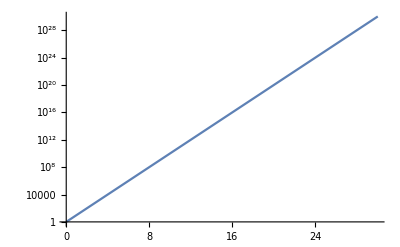

```mathematica
LogPlot[10^x,{x,0,30},PlotRange->All]
```

```mathematica
?LogPlot
```

LogPlot[f,{x,x_min,x_max}] generates a log plot of f as a function of x from x_min to x_max. 
LogPlot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i. 
LogPlot[{…,w[f_i],…},…] plots f_i with features defined by the symbolic wrapper w.
LogPlot[…,{x}∈reg] takes the variable x to be in the geometric region reg.

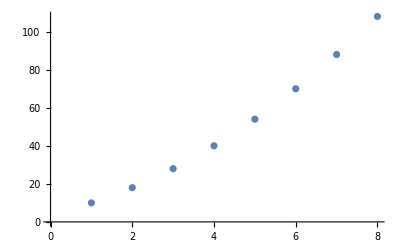

```mathematica
ListPlot[Table[i^2+3i,{i,2,9}]]
```

{{1,1},{3,27},{5,125},{7,343},{9,729},{11,1331},{13,2197},{15,3375},{17,4913},{19,6859}}

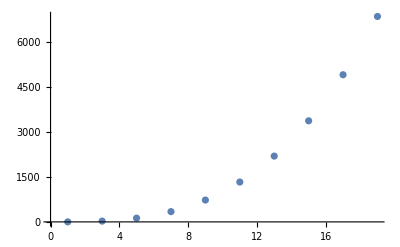

```mathematica
t=Table[{2i+1,(2i+1)^3},{i,0,9}]
ListPlot[t]
```

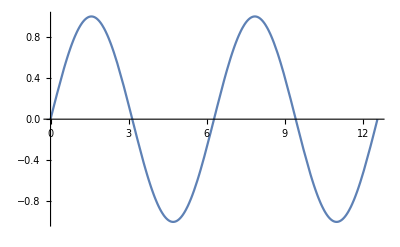

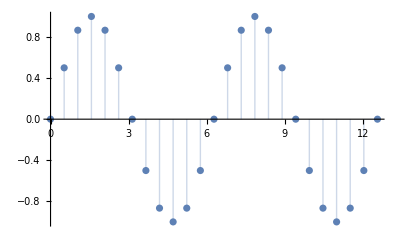

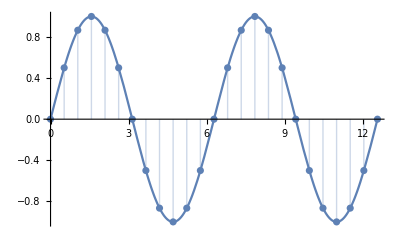

```mathematica
a=Plot[Sin[x],{x,0,4Pi}]
b=ListPlot[Table[{x,Sin[x]},{x,0,4Pi,Pi/6}],Filling->Axis]
Show[a,b]
```

-Graphics-

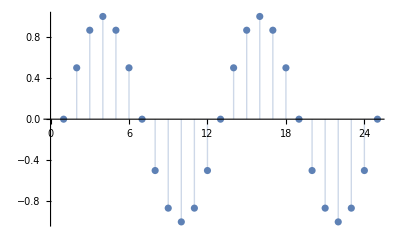

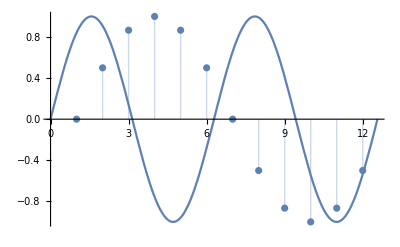

```mathematica
a=Plot[Sin[x],{x,0,4Pi}]
b=ListPlot[Table[Sin[x],{x,0,4Pi,Pi/6}],Filling->Axis]
Show[a,b]
```

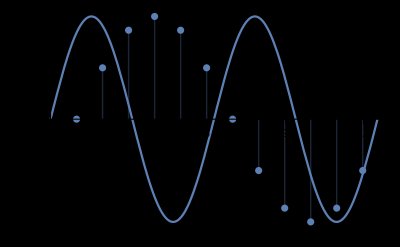

```mathematica
Show[%25,Background->Black]
```

```mathematica
Show[%26,Background->White]
```

-Graphics-

```mathematica
Animate[Graphics[Disk[{5Cos[60 Degree]t,5Sin[60 Degree]t-1/2 9.8t^2},5/100],PlotRange->{{0,2.5},{0,1}}],{t,0,1}]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
Clear[y]
```

```mathematica
Coefficient[(2x+y)^6,x^(4)y^4]
```

0

```mathematica
a^3b^2
```

a^3 b^2

```mathematica
{3,I,-7,h,Pi,7/11}[[4]]
```

h

```mathematica
Remove[h]
```

```mathematica
a={{1,2,3},{Pi,4,-7},{I,4,6}};
a[[1]]
a[[2,1]]
a[[2]][[1]]
```

{1,2,3}

π

π

```mathematica
Solve[{2x-3y==4,6x+7y==1},{x,y}]
{2x-3y,6x+7y}/.Solve[{2x-3y==4,6x+7y==1},{x,y}]
```

{{x→31/32,y→-11/16}}

{{4,1}}

```mathematica
Sin[x]+x/.Solve[2x^2-3x==0][[2]]
```

```mathematica
3/2+Sin[3/2]Vi[
```

```mathematica
Vi Cos[th]t/.Solve[Vi Sin[th]t-1/2g t^2==0,t][[2]]
```

(2 Vi^2 Cos[th] Sin[th])/g

```mathematica
range[vi_,th_]:= (tp=t/.Solve[vi Sin[th]t-1/2g t^2==0,t][[2]];vi Cos[th]tp); range[vi,th]
"Calling with Initial Velocity"
range[4.5,th]
"Repeat with Angle & Initial velocity"
Do[Print[range[4.5,i]],{i,0,2Pi,Pi/8}]
```

(2 vi^2 Cos[th] Sin[th])/g

Calling with Initial Velocity

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(40.5 Cos[th] Sin[th])/g

Repeat with Angle & Initial velocity

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

14.3189/g

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

20.25/g

14.3189/g

0.

-14.3189/g

-20.25/g

-14.3189/g

0.

14.3189/g

20.25/g

14.3189/g

0.

-14.3189/g

-20.25/g

-14.3189/g

0.

```mathematica
?Do
```

Do[expr,n] evaluates expr n times. 
Do[expr,{i,i_max}] evaluates expr with the variable i successively taking on the values 1 through i_max (in steps of 1). 
Do[expr,{i,i_min,i_max}] starts with i=i_min. 
Do[expr,{i,i_min,i_max,di}] uses steps di. 
Do[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Do[expr,{i,i_min,i_max},{j,j_min,j_max},…] evaluates expr looping over different values of j etc. for each i.

```mathematica
range[vi_,th_]:= (tp=t/.Solve[vi Sin[th]t-1/2g t^2==0,t][[2]];vi Cos[th]tp); range[vi,th]
"Calling with Initial Velocity"
range[4.5,th]
"Repeat with Angle & Initial velocity"
Do[Print[range[2,i]],{i,0,2Pi,Pi/8}]
```

(2 vi^2 Cos[th] Sin[th])/g

Calling with Initial Velocity

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(40.5 Cos[th] Sin[th])/g

Repeat with Angle & Initial velocity

0

(8 Cos[π/8] Sin[π/8])/g

4/g

(8 Cos[π/8] Sin[π/8])/g

0

-(8 Cos[π/8] Sin[π/8])/g

-4/g

-(8 Cos[π/8] Sin[π/8])/g

0

(8 Cos[π/8] Sin[π/8])/g

4/g

(8 Cos[π/8] Sin[π/8])/g

0

-(8 Cos[π/8] Sin[π/8])/g

-4/g

-(8 Cos[π/8] Sin[π/8])/g

0

WolframAlphaQueryNoResults

URLFetch::invhttp: Could not resolve host: api.wolframalpha.com.

```mathematica
?=.
```

lhs=. removes any rules defined for lhs.

```mathematica
g=Solve[k 3 10^-2==5,k];k=k/.g[[1]];
NIntegrate[-k x,{x,0.07,0.11}]
```

-0.6